```mathematica
(* Looking at Entropy *)
Manipulate[Plot[{(1-2*Abs[p-.5]),1/(1-a)*Log2[p^a+(1-p)^a]},{p,0,1}],{a,0.01,10}]
```

```mathematica
Id :={{1,0},{0,1}}
Z:={{1,0},{0,-1}}
X:={{0,1},{1,0}}
Y:={{0,-ⅈ},{ⅈ,0}}
```

```mathematica
Initial=MatrixForm[Outer[Times,Z,Id]]
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1))

```mathematica
M = MatrixForm[Outer[Times,Z,Id]];
M.Initial.M
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1)).((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1)).((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1))

```mathematica
(* PDEs for random circuit *)
pde=D[S[y,t],t]==b/2 * (1-D[S[y,t],y]^2)
soln=DSolve[pde,S[y,t],{y,t}]
```

S^(0,1)[y,t]==1/2 b (1-(S^(1,0)[y,t])^2)

DSolve::nlpde: Solution requested to nonlinear partial differential equation. Trying to build a special solution.

{{S[y,t]→C[1]-(y √(b-2 C[2]))/(√b)+t C[2]},{S[y,t]→C[1]+(y √(b-2 C[2]))/(√b)+t C[2]}}

```mathematica
Clear[S,t,y]
NDSolve[{D[S[y,t],t]==(1/4) *(1-(D[S[y,t],y])^2),S[y,0]==0,S[0,t]==0, S[10,t]==0},S[y,t],t]
```

NDSolve::underdet: There are more dependent variables, {S[0,t],S[10,t],S[y,t],S^(1,0)[y,t]}, than equations, so the system is underdetermined.

NDSolve[{S^(0,1)[y,t]==1/4 (1-(S^(1,0)[y,t])^2),S[y,0]==0,S[0,t]==0,S[10,t]==0},S[y,t],t]

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}];
Plot3D[Evaluate[u[t,x]/.%],{t,0,10},{x,0,5},PlotRange->All]
```

-Graphics3D-

```mathematica
(* Transition Matrices *)
(* 1-staircases *)
P1 = {{1-(1+m)/2 Γ, (1+m)/2 Γ, 0, 0},{0,1-Γ,Γ,0},{(1-m)/2 Γ, 0, 1-Γ, (1+m)/2 Γ},{0,(1-m)/2 Γ, 0, 1-(1-m)/2 Γ}}//Transpose;
(P1-IdentityMatrix[4])/Γ//MatrixForm
```

(1/2 (-1-m) | 0 | (1-m)/2 | 0
(1+m)/2 | -1 | 0 | (1-m)/2
0 | 1 | -1 | 0
0 | 0 | (1+m)/2 | 1/2 (-1+m))

```mathematica
m = 0.1;
Γ = .9;
MatrixPower[P1,100]//MatrixForm
Clear[m,Γ]
```

(0.2025 | 0.2025 | 0.2025 | 0.2025
0.2475 | 0.2475 | 0.2475 | 0.2475
0.2475 | 0.2475 | 0.2475 | 0.2475
0.3025 | 0.3025 | 0.3025 | 0.3025)

```mathematica
Eigenvectors[P1];
```

```mathematica
(* 2-Staircase *)
(* 3-site *)
ThreeSite = 
{{3,0,0,0,0,0,0,0},
{0,1,0,0,2,0,0,0},
{0,2,1,0,0,0,0,0},
{0,0,0,1,0,1,1,0},
{0,0,2,0,1,0,0,0},
{0,0,0,1,0,1,1,0},
{0,0,0,1,0,1,1,0},
{0,0,0,0,0,0,0,3}};
Map[MatrixForm,JordanDecomposition[ThreeSite]]
```

{(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1/2 (-1+ⅈ √3) | 1/2 (-1-ⅈ √3)
0 | 0 | 0 | 0 | 1 | 0 | 1/2 (-1-ⅈ √3) | 1/2 (-1+ⅈ √3)
-1 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ √3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ √3)}

```mathematica
Trans = 
{{1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0},
{0,0,0,0,1,0,0,0},
{0,0,0,1,0,0,0,0},
{0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,1}};
MatrixForm[Trans.ThreeSite.Trans]
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

```mathematica
(* 4-site *)
FourSiteSmall = {{1/2, 0, 0, 1/4,1/2, 0},{1/4, 0, 0, 0, 0, 1/4}, {1/4, 1/2, 1/2, 0, 0, 0},{ 0, 1/2, 0, 1/2, 0, 1/4}, {0, 0, 1/4, 1/4, 0, 0}, {0, 0, 1/4, 0, 1/2, 1/2}};
MatrixForm[N[MatrixPower[FourSiteSmall,30]]]
Eigenvalues[FourSiteSmall]
```

(0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1
0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2)

{1,1/2+ⅈ/4,1/2-ⅈ/4,1/8 (1+ⅈ √15),1/8 (1-ⅈ √15),-1/4}

```mathematica
SixSite =
{{4,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0},{1,2,0,0,0,0,0,0,0,0,0,0,0,1,2,0,0,0,0,0},{1,1,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0},{0,1,2,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
{0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0},
{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},
{0,0,0,1,1,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,1},
{0,0,0,1,0,0,1,2,2,0,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,2,4,0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,2,0,0,0,0,0,4,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,2,0,0,0,0,1,2,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,2,0,0,0,1,1,2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0,0,2,0,2,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,1,0,2,2,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,2,0,0,4,0,0,0},
{0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,0,1,2,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,2,2,0},
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,4}};
S = Eigenvectors[SixSite][[1]]
```

{20,12,14,20,14,7,12,12,14,20,20,12,14,14,7,12,20,12,14,20}

```mathematica
Total[S]
```

290

```mathematica
MatrixPlot[SixSite]
```

```mathematica
(* All States *)
threeA = 
{{1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,1,0,1,0,0,0},
{0,0,0,0,0,0,0,0},
{0,0,0,1,0,1,1,0},
{0,0,0,0,0,0,0,1}};
```

```mathematica
S = {{1,0,0,0},
    {0,0,1,0},
    {0,1,0,0},
    {0,0,0,1}};
eye = {{1,0},{0,1}};
S3 = KroneckerProduct[eye,S].KroneckerProduct[S,eye];
```

```mathematica
KroneckerProduct[threeA ,eye]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
DigitCount[5,2,1]
```

2

{{1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1}}

1

1/2 (1-x^2+1/2 (3+x) (1-x^2))

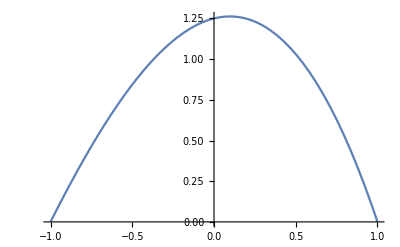

```mathematica
(* Growth Rates for Uncorrelated Staircase Circuits *)
Γ = 1
y = Γ/2(1-x^2+(1-x^2)/2(3+x))
Plot[y, {x,-1,1}]
```

```mathematica
(* Growth Rates Recurrence Relationship *)

R[0,m_]:= 0
R[n_,m_] := R[n-1, m] + (1+m)  - 2*((1+m)/2)^(n+1)
Rate[n_,m_] := R[n,m]/n
Factor[Rate[2, m]]
```

-1/8 (-1+m) (1+m) (5+m)

```mathematica
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
FortranForm[Rate[6, ms]/.E^x_:>exp[x]]
SetOptions[$Output,PageWidth->pw];
```

(6 + 6*ms - (1 + ms)**2/2. - (1 + ms)**3/4. - (1 + ms)**4/8. - (1 + ms)**5/16. - (1 + ms)**6/32. - (1 + ms)**7/64.)/6.

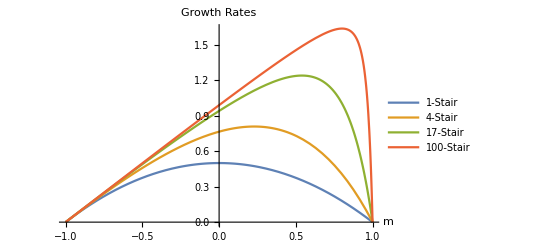

/Users/cstahl/Documents/Senior/Thesis

figures/analrates.pdf

```mathematica
p1=Plot[{Rate[1,m],Rate[4,m],Rate[17,m],Rate[100,m]}, {m,-1,1},PlotLegends->{"1-Stair","4-Stair","17-Stair","100-Stair"}, PlotLabel->Style["Growth Rates",16], AxesLabel->{Style[m,16]}]
SetDirectory[NotebookDirectory[]]
Export["figures/analrates.pdf",p1]
```

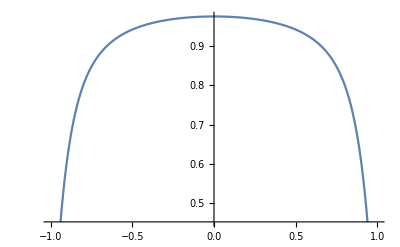

```mathematica
n = 40;
Plot[(Rate[n,m]+Rate[n,-m])/2,{m,-1,1}]
```

```mathematica
Factor[Rate[6,m]]
```

-1/384 (-1+m) (1+m) (321+201 m+102 m^2+38 m^3+9 m^4+m^5)

```mathematica
(* Entanglement Curves *)
(* Legendre Transforms *)
```

```mathematica
(* 2-Stair *)
Clear[Γ,m,v,G,S,M,t]
Γ[m_] := (1-m^2)/2*(5+m)/2;
v[m_] := (3m^2+10m-1)/4;
Maximize[{Γ[m]+m*vv, m^2<1}, vv]
Γ[m]+m*v[m]
(*m[l_] :=1/3 (-5+2 Sqrt[7+3 l]);
G[v_]   := Γ[m[v]]-v*m[v]
S=FullSimplify[G[x/t]]*t
M = D[S,x];
FullSimplify[(1-M^2)/2*(5+M)/2-D[S,t]]
FullSimplify[v[m[t]]]*)
```

{Piecewise[{{5/4, m==0}, {-∞, !(m==0||-1<m<0||0<m<1)}, {∞, True}}],{vv→Piecewise[{{Indeterminate, m≠0}, {0, True}}]}}

1/4 (5+m) (1-m^2)+1/4 m (-1+10 m+3 m^2)

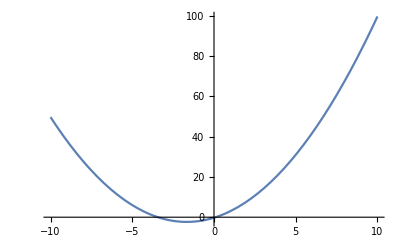

```mathematica
Plot[v[m],{m,-10,10}]
```

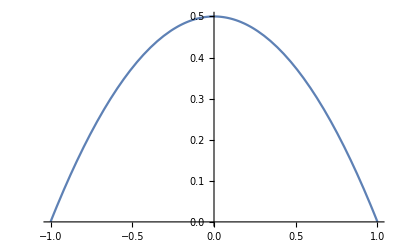

t (Piecewise[{{1/2, x==0&&t≠0}, {Indeterminate, t==0}, {-x/t, (t>0&&t+x<0)||(t<0&&t+x>0)}, {x/t, (t>0&&t<x)||(t<0&&t>x)}, {1/2 (1+x^2/t^2), True}}])

-Graphics-

Piecewise[{{Indeterminate, t==0}, {0, True}}]

```mathematica
(* 1-Stair *)
Clear[Γ,m,v,G,S,M,t]
Γ[m_] := (1-m^2)/2;
Plot[Γ[m],{m,-1,1}]
m[v_]:=ArgMax[{Γ[m]+m v,-1≤m≤1},m];
G[v_]   := Γ[m[v]]+v*m[v];
S=FullSimplify[G[x/t]]*t
Manipulate[Plot[S,{x,-2,2}],{t,1,2}];
Plot[S,{x,-2,2}]
M = D[S,x];
FullSimplify[(1-M^2)/2-D[S,t]]
```